# UV Hygrometer WECAN

## 2019-01-10

Calculate high-rate UV Hygrometer mixing ratio.
Using fit parameters derived from the low rate data, in WECAN_UVHygrometer_FitParameters.txt

See the low-rate fit file (uvhFit_rf01.nb) for complete description of process and variables.

## Initialization

```mathematica
ClearAll[Evaluate[$Context<>"*"]]
SetDirectory[NotebookDirectory[]];
```

```mathematica
kB=QuantityMagnitude[UnitConvert[Quantity["BoltzmannConstant"]]];
```

```mathematica
(* The equation for number density (molecules/m^3) with the fit parameters determined by the low-rate data. This fit had a factor of 10^22 factored out of the density. *)
densityEqn[v_]=10^22/-σl Log[(v-a)/b];
(* Values calculated from low-rate fit, after hand adjustment as necessary. *)
{flightNumber, dropAtStart, linearDecayRate,linearDecayStartTime, a, b, σl}={1,2000,-1.0*^-6,68809,0.43,3.28,0.0989};
```

```mathematica
(* Data file names: high rate (HR) for temp/signal reduced to 25 Hz from 100 Hz, and sample rate for pressure (recorded only at 10 Hz. *)
(* NOTE: header must be deleted from dataFiles! *)
datafileHR="/Users/Shared/BigStuff/WecanData/xTempSigRF01h.txt";
datafileSR="/Users/Shared/BigStuff/WecanData/xpresRF01s.txt" ; (* For pressure data only. *)
exportFileHR="uvh_rf01h.txt";
```

## Start and stop times for high rate file.

```mathematica
startTimeHR=70000.0;
stopTimeHR=89800.0;
```

## Read data.

### Import data from high-rate file for signal and temperature (25 sps)

```mathematica
dataHR=Import[datafileHR,"CSV"]; (* NOTE: header must be deleted from file!. *)
dataHR[[All,2]] +=273.15; (* Convert temperature to kelvin *)

(* If seconds rolls over, find rollover index and add 24x3600=86400 seconds to time. *)
iROLLOVER=Flatten[Position[dataHR[[All,1]],0.0]][[1]];
If[IntegerQ[iROLLOVER],dataHR[[iROLLOVER;;-1,1]]+=86400;,"No seconds rollover"]

(* Set start and stop times of high-rate data. *)
iSTART=Flatten[Position[dataHR[[All,1]],startTimeHR]][[1]];
If [IntegerQ[iSTART],"Shortening dataHR at start",{iSTART=1;"No data drop at start"}]

iEND=Flatten[Position[dataHR[[All,1]],stopTimeHR]][[1]];
If [IntegerQ[iEND],"Shortening dataHR at end",{iEND=-1;"No data drop at end"}]

"Using high-rate data from indices:"
{iSTART,iEND}
dataHR=dataHR[[iSTART;;iEND]];
Dimensions[dataHR]
```

Shortening dataHR at start

Shortening dataHR at end

Using high-rate data from indices:

{40001,535001}

{495001,3}

```mathematica
ListPlot[Transpose[{dataHR[[All,1]],dataHR[[All,2]]}],Joined->True]
```

-Graphics-

```mathematica
ListPlot[Transpose[{dataHR[[All,1]],dataHR[[All,3]]}],PlotRange->{{88000,90000},Automatic},Joined->True]
```

-Graphics-

### Import data from sample-rate file for pressure (at 10 sps).

```mathematica
xcellpresSR=Import[datafileSR,"CSV"]; (* NOTE: header must be deleted from file!. *)
xcellpresSR[[All,2]]*=100; (* Convert hPa to Pa. *)

(*Repeat time checks above.*)
(* If seconds rolls over, find rollover and add 24x3600=86400 seconds to time. *)
iROLLOVER=Flatten[Position[xcellpresSR[[All,1]],0.0]][[1]]
If[IntegerQ[iROLLOVER],xcellpresSR[[iROLLOVER;;-1,1]]+=86400;,"No seconds rollover"]

(* Set start and stop times of high-rate data. *)
iSTART=Flatten[Position[xcellpresSR[[All,1]],startTimeHR]][[1]]
If [IntegerQ[iSTART],"Shortening dataHR at start",{iSTART=1;"No data drop at start"}]

iEND=Flatten[Position[xcellpresSR[[All,1]],stopTimeHR]][[1]]
If [IntegerQ[iEND],"Shortening dataHR at end",{iEND=-1;"No data drop at end"}]

xcellpresSR=xcellpresSR[[iSTART;;iEND]];
Dimensions[xcellpresSR]
```

279191

115191

Shortening dataHR at start

313191

Shortening dataHR at end

{198001,2}

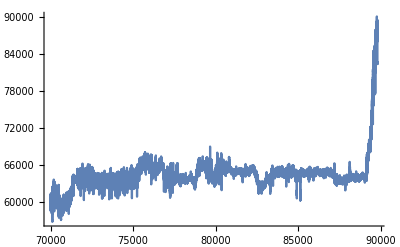

```mathematica
ListPlot[xcellpresSR,Joined->True,PlotRange->All]
```

### Interpolate pressure data from 10 Hz to 25 Hz.

```mathematica
xcellpresFn=ListInterpolation[xcellpresSR[[All,2]]];
```

```mathematica
(* Since the pressure data was at 10 Hz, interpolating at 0.40 will give 0.040 s/sample, = 25 Hz. *)
xcellpresHR=xcellpresFn[Table[i,{i,1,Length[xcellpresSR],0.40}]]; 
Dimensions[xcellpresHR]
```

{495001}

```mathematica
(* Variable to make plotting easier. Consists of {time,value}. *)
xcellpresPlotHR=Transpose[{dataHR[[All,1]],xcellpresHR}];
```

```mathematica
ListPlot[{xcellpresSR,xcellpresPlotHR},PlotRange->{{80000,80003},{63700,64100}},Joined->{False,True} , PlotStyle->{Red,Blue}, ImageSize->Scaled[0.8]]
```

-Graphics-

## Calculations

### Invert for number density from Voltage

Reread the .nc file for time and uvh values to calculate mixing ratio without any gaps.

```mathematica
(* Adjust signal voltage for lamp decay, window dirtying. *)
temp=Table[dataHR[[i,3]]+linearDecayRate*(dataHR[[i,1]]-linearDecayStartTime),{i,1,Length[dataHR]}];

(* Adjust signal voltage for pressure (O2 adsorption). *)
xsigvAdjHR=temp/Exp[-0.25*xcellpresHR*10^-5];
Clear[temp];
```

```mathematica
(* Calculate number density in hygrometer cell based on adjusted voltage signal. *)
densityCalc=densityEqn[xsigvAdjHR];
cellNumberDensity=xcellpresHR/(dataHR[[All,2]]*kB);
MR=densityCalc/cellNumberDensity;
MRPlot=Transpose[{dataHR[[All,1]],MR}];
```

```mathematica
ListPlot[MRPlot,PlotStyle->{Red,Blue},Frame->True,FrameLabel->{"Time","MR"},Joined->True,ImageSize->Full]
```

-Graphics-

### Export High-rate mixing rate data in ppm.

Multiply calculated mixing ratio by 10^6 to get ppmv. 
As post-processing the file needs to have the curly brackets removed and line returns added.

```mathematica
exportData=Transpose[{MRPlot[[All,1]],MRPlot[[All,2]]*1000000.0}];
```

```mathematica
(*NumberForm to get enough digits and in non-scientific. Need 2 digits in time to get 0.04 s resolution. *)
Export[exportFileHR, NumberForm[exportData,{8,2}],"Table"]
```

uvh_rf01h.txt